# Rb87 Calculations

## Constants

```mathematica
(*get from local files*)
SetDirectory[NotebookDirectory[]];
<<"../constants/rbconsts.m"
<<"../constants/physconsts.m"
EHFeV = JToeV[EHF];
```

### Conversions

```mathematica
GHzToJ[ν_]:=10^9 h ν;
GHzToeV[ν_]:=(10^9 h ν)/e 
JToGHz[u_]:=u/(10^9 h);
JToMHz[u_]:=u/(10^6 h);
JToeV[u_]:=u/e;
eVToGHz[u_]:=e/(10^9 h)u;
```

## Misc. Functions

Conversion functions, for explicitly followable unit changes in the code, at the risk of handicapping myself later.

## Zeeman shifts

### Ground state hyperfine level shifts

This calculation seems only first order, and doesn’t seem to actually be diagonalizing the Hamiltonian in general. Why this not do like Python??

```mathematica
Clear[J,L,F,FF,mF,mFF]
```

```mathematica
HFZeemanMatElem[I_,J_,gJ_,{F_,mF_},{FF_,mFF_},q_,Bz_]:=KroneckerDelta[mF,mFF]μB Bz (ClebschGordan[{F,mF},{1,q},{FF,mFF}] √(2 F +1)(-1)^(1+J+I)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,I,F},{FF,1,J}]+
gI(-1)^FF √(I(I+1)(2I+1))SixJSymbol[{I,J,F},{FF,1,I}]));
```

```mathematica
S = 1/2; L = 0; J = 1/2;
gJ=gL(J(J+1)+L(L+1)-S(S+1)
+gS(J(J+1)-L(L+1)+S(S+1)))/(2J(J+1));
gF[F_]:= (gJ(F(F+1)+J(J+1)-I(I+1))
+gI(F(F+1)-J(J+1)+I(I+1)))/(2F(F+1));
```

```mathematica
States = Flatten[Table[Table[{F,mF},{mF,-F,F}],{F,{2,1}}],1];
```

Compute Hamiltonians in eV to avoid ridiculously small numbers

```mathematica
q=0; dim = Length[States];
HZ1[Bz_]=Table[Table[JToeV[HFZeemanMatElem[INuc,J,gJ,States[[i]],States[[j]],q,Bz]],{i,1,dim}],{j,1,dim}];
```

ClebschGordan::phy: ThreeJSymbol[{2,-1},{1,0},{2,2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2,0},{1,0},{2,2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2,1},{1,0},{2,2}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

```mathematica
HAtom = EHFeV{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
```

```mathematica
HTotal[B_]=HAtom + HZ1[B];
ZShifts[B_]=Eigenvalues[HTotal[B]];(*Eigenenergies [eV]*)
```

```mathematica
(*BList = Range[0,0.5,.1];
ZShiftsData = Range[0,Length[ShiftsMat]];
ZShiftsMat = Transpose@Table[ZShifts[B],{B,BList}];
For[i = 0, i< Length[ZShiftsMat],i++,
	ZShiftsData[[i]] = Transpose@{BList,Sort[[ZShiftsMat[[i]]]]}
]*)
```

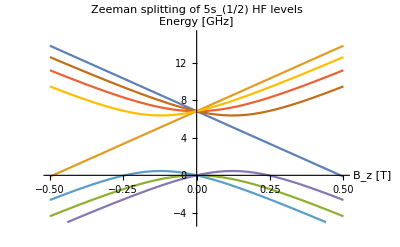

```mathematica
Bmax = 0.5; (*[T]*)
Plot[Evaluate[eVToGHz[Sort[ZShifts[B],Greater]]],{B,-Bmax,Bmax},PlotRange->{{-Bmax,Bmax},{-5,15}},PlotLabel->"Zeeman splitting of 5s_(1/2) HF levels ",AxesLabel->{"B_z [T]","Energy [GHz]"}]
```

0.001

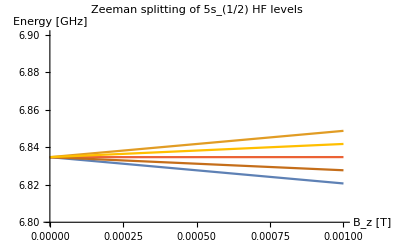

```mathematica
Bmax=0.001
Plot[Evaluate[eVToGHz[Sort[ZShifts[B],Greater]]],{B,0,Bmax},PlotRange->{{0,Bmax},{6.8,6.9}},PlotLabel->"Zeeman splitting of 5s_(1/2) HF levels ",AxesLabel->{"B_z [T]","Energy [GHz]"}]
```

### Differential Hyperfine Shifts

m=0,m’=0 has a quadratic shift

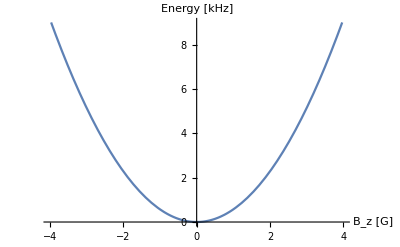

```mathematica
Plot[eVToGHz[ZShifts[10^-4 B][[4]]-EHFeV-ZShifts[10^-4 B][[3]]]/10^-6,{B,-4,4},PlotLabel->"",AxesLabel->{"B_z [G]","Energy [kHz]"},PlotRange->{0,9}]
```

F=2,m=0,F=1,m=1

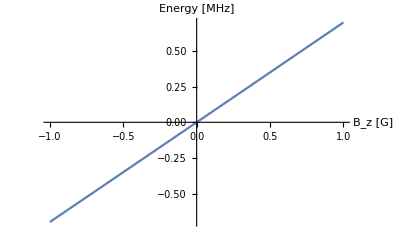

```mathematica
Plot[eVToGHz[ZShifts[10^-4 B][[4]]-EHFeV-ZShifts[10^-4 B][[7]]]/10^-3,{B,-1,1},PlotLabel->"",AxesLabel->{"B_z [G]","Energy [MHz]"}]
```

For a given Bz, the scalar Zeeman shifts are as a function of some field in the cylindrical radial direction ρ. The plot below shows the frequency offset (from the degenerate hyperfine resonance) needed to drive  F=2,m=0,F=1,m=1.

```mathematica
Manipulate[Plot[eVToGHz[ZShifts[10^-4 √(Bz^2+Bρ^2)][[4]]-EHFeV-ZShifts[10^-4 √(Bz^2+Bρ^2)][[7]]]/10^-3,{Bρ,-.4,.4},AxesLabel->{"B_ρ [G]","Energy [MHz]"},PlotLabel->"f_offset 2,0->1,1 from degenerate HF resonance",PlotRange->{2.69,2.72}],{Bz,0,4}]
```

Part::partw: Part 4 of ZShifts[0.000386078] does not exist.

Part::partw: Part 7 of ZShifts[0.000386078] does not exist.

Part::partw: Part 4 of ZShifts[0.000385912] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of ZShifts[0.000386078] does not exist.

Part::partw: Part 7 of ZShifts[0.000386078] does not exist.

Part::partw: Part 4 of ZShifts[0.000385912] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of ZShifts[0.000386078] does not exist.

Part::partw: Part 7 of ZShifts[0.000386078] does not exist.

Part::partw: Part 4 of ZShifts[0.000385912] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of ZShifts[0.000386078] does not exist.

Part::partw: Part 7 of ZShifts[0.000386078] does not exist.

Part::partw: Part 4 of ZShifts[0.000385912] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of ZShifts[0.000386078] does not exist.

Part::partw: Part 7 of ZShifts[0.000386078] does not exist.

Part::partw: Part 4 of ZShifts[0.000385912] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of ZShifts[0.000386078] does not exist.

Part::partw: Part 7 of ZShifts[0.000386078] does not exist.

Part::partw: Part 4 of ZShifts[0.000385912] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of ZShifts[0.000386078] does not exist.

Part::partw: Part 7 of ZShifts[0.000386078] does not exist.

Part::partw: Part 4 of ZShifts[0.000385912] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

### Atom Magnetometry

Summer 2019. Most of this is toward the goal of effectively canceling environmental magnetic fields with our shim coils, as verified by measuring Zeeman shifts for various ground state hyperfine transitions.

Deduce Bρ given two resonances for F=2,m=0 to F=1,m=1 measured for two different Bz. Bz coils were first set to some value Bz, and resonance at f_offset = 2.7144 MHz, then to Bz/2, with f_offset = 1.3697 MHz.

```mathematica
F2m0ToF1m1Offset[Bz_,Bρ_]:=eVToGHz[ZShifts[10^-4 √(Bz^2+Bρ^2)][[4]]-EHFeV-ZShifts[10^-4 √(Bz^2+Bρ^2)][[7]]]/10^-3
```

```mathematica
eVToGHz[-ZShifts[10^-4 √(Bz^2+Bρ^2)][[7]]]/10^-3//FullSimplify
```

-3417.34+0.00139064 √(Bz^2+Bρ^2)+0.403213 √(7.18304×10^7+12.0295 Bz^2+12.0295 Bρ^2+29395.3 √(Bz^2+Bρ^2))

Given two measured offsets corresponding to Bz and Bz/2, solve for Bz neglecting the F=2,m=0 shift.

```mathematica
fFullZShim = -2.71; fHalfZShim = -1.371;
Solve[eVToGHz[-ZShifts[10^-4 √(BzSq+Bρ^2)][[7]]]/10^-3==fFullZShim,BzSq]//FullSimplify
```

{{BzSq→14.9965-1. Bρ^2},{BzSq→5.97602×10^6-1. Bρ^2}}

```mathematica
Solve[-3417.3413054521443+0.0013906403370048004 √(BzSq/4+Bρ^2)+0.40321259623427075 √(7.183044056176053*^7+12.029488171690414 BzSq/4+12.029488171690414 Bρ^2+29395.296139093578 √(BzSq/4+Bρ^2))==fHalfZShim,BzSq]//FullSimplify
```

{{BzSq→15.3347-4. Bρ^2},{BzSq→2.39416×10^7-4. Bρ^2}}

```mathematica
Solve[14.996478293557628-1. Bρ^2==15.334695262703281-4. Bρ^2,Bρ](*Bρ [G]*)
```

{{Bρ→-0.335766},{Bρ→0.335766}}

This gives Bρ; what is Bz given this with a shift of -1.371 MHz?

```mathematica
Bρ = 0.33576;
NSolve[eVToGHz[-ZShifts[10^-4 √(Bz^2+Bρ^2)][[7]]]/10^-3==2.71,Bz]
```

{{Bz→-3.84875},{Bz→3.84875}}

```mathematica
{{Bz->-3.8487451864981783},{Bz->3.8487451864981765}}
```

```mathematica
B = √(Bρ^2+3.848745^2)
```

3.86336

What if there is an environmental field along Z?

```mathematica
Clear[Bz0,Bz]
```

```mathematica
NSolve[{-3417.3413054521443+0.0013906403370048004 √((Bz/2+Bz0)^2+Bρ^2)+0.40321259623427075 √(7.183044056176053*^7+12.029488171690414 (Bz/2+Bz0)^2+12.029488171690414 Bρ^2+29395.296139093578 √((Bz/2+Bz0)^2+Bρ^2))==1.371 ,-3417.3413054521443+0.0013906403370048004 √((Bz+Bz0)^2+Bρ^2)+0.40321259623427075 √(7.183044056176053*^7+12.029488171690414 (Bz+Bz0)^2+12.029488171690414 Bρ^2+29395.296139093578 √((Bz+Bz0)^2+Bρ^2))==2.71},{Bz,Bz0}]//FullSimplify
```

{{Bz→11.5507,Bz0→-7.70193},{Bz→-11.5507,Bz0→7.70193},{Bz→3.84431,Bz0→0.00443971},{Bz→-3.84431,Bz0→-0.00443971}}

With the field zeroed in x and y, B_environment=Bz0 above. What is the m0->m1 shift for this value?

Two experiments with slightly different Y shims yield different resonances, so we can deduce the change in scalar field.

```mathematica
Bz0 = -0.00443971;
eVToGHz[ZShifts[10^-4 Bz0][[4]]-EHFeV-ZShifts[10^-4 Bz0][[7]]]/10^-6 (*[kHz]*)
```

-3.1106

```mathematica
NSolve[eVToGHz[-ZShifts[10^-4 B1][[7]]]/10^-3==-1.3685,B1]
```

{{B1→-2446.51},{B1→-1.9544}}

```mathematica
NSolve[eVToGHz[-ZShifts[10^-4 B2][[7]]]/10^-3==-1.3721,B2]
```

{{B2→-2446.5},{B2→-1.95955}}

```mathematica
Abs[1.95955-1.9544] (*change in scalar field [G]*)
```

0.00515

7/23/19 - Measuring the hyperbolic m=0 to m=0 shift to find any environmental bias in Z. There should be about 4.4 mG as calculated above.

4.35354-0.107686 z+54.6076 z^2

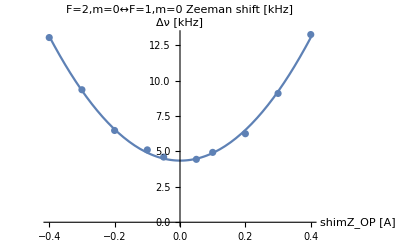

```mathematica
m0m0ShiftData = {{-0.4,13.043},{-0.3,9.357},{-.2,6.481},{-.1,5.111},{-.05,4.602},{.05,4.443},{.1,4.934},{.2,6.251},{.3,9.096},{.4,13.255}};
fit[z_] =Fit[m0m0ShiftData,{1,z,z^2},z]
Show[ListPlot[m0m0ShiftData,AxesLabel->{"shimZ_OP [A]","Δν [kHz]"},PlotLabel->"F=2,m=0↔F=1,m=0 Zeeman shift [kHz]"],Plot[fit[z],{z,-.4,.4}]]
```

```mathematica
Minimize[fit[z],z]
```

{4.35349,{z→0.000985998}}

The offset should be due to the AC Stark shift from the FORT. Calculate this in Optical Trapping/FORT.

## Laser Cooling and Trapping

### Optical Molasses

```mathematica
Is = g1/g2(ℏ γD2 ωD2^3)/(12 π c^2) ;g1 = 5; g2 = 7;(*saturation intensity. gi = ith state degeneracy*)
```

```mathematica
β[Δ_,I_]:=8ℏ kD2^2(-Δ/γD2)/((1+4 Δ^2/γD2^2)^2)I/Is;(*s set to 1*)
F[Δ_,I_]:= (ℏ kD2 γD2)/2 I/Is 1/(1+(4 Δ^2)/γD2^2+I/Is);
```

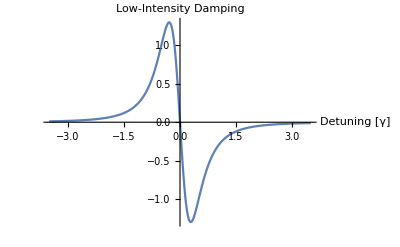

```mathematica
Plot[β[Δ*γD2,Is]/(ℏ kD2^2),{Δ,-3.5,3.5},PlotRange-> Full,AxesLabel->{"Detuning [γ]","Low-Intensity Damping"}]
```

Cool atoms into optical molasses.
Program:
	- Generate array of atoms with gaussian velocity dist O(1 m/s),
	a random initial state either e or g,F where F=2,1 are the 
	hyperfine levels.
	- For[t = 0, t < t_exp, t+=dt,
		For[i = 0, i< # of atoms, i++,
			x = v*t + .5 (F[v]/m) t^2
			if RandomReal > decays/dt  // not quite
				state = |g,F = Random[1 or 2] >	
		]
		If i mod int(t_exp/shots)
			ListPlot[Transpose@{atom_positions,atom_velocities}]
	  ]

```mathematica
pts = NormalRandoms[0,2,10,10]
```

$Aborted

#### Sensitivity to beam imbalance

An atom in our FORT during RO is exposed to the MOT light for ~ (1-.53)*8*10^-7 s

```mathematica
d=.53
```

0.53

```mathematica
tFree =(1-d)*8*10^-7;
fChop= 1.25*10^6;
tRO = 2*10^-3;(*5*10^-3;*)
tTotal= tFree*fChop*tRO
```

0.00094

MOT intensity per arm:

```mathematica
IMOT = (5*10^-4)/(π (.005)^2) ;(*Assumes 1mm wide circular beams, ~.5mW*)
```

Consider two beams of a MOT with differing intensities.

```mathematica
FNet[I1_,I2_] := F[-3 γD2,I1]-F[-3 γD2,I2];
```

```mathematica
Clear[t]
```

```mathematica
Manipulate[Plot[(1/2 FNet[α s,.9 α*s]/mRb ((1-duty)*8*10^-7)^2)/10^-6,{α,.1,1},AxesLabel->{"I_Rel","Distance traveled"}],{duty,.3,.8}]
```

### Magneto-Optical Trap

For good PGC, make Ω^2/Δγ

```mathematica
Int = P/(π w0^2); P =2.5*10^-3; w0=2*10^-3;Δ =-5* ΓD2;ΩSq = (2 *Int)/(c ϵ0 ℏ^2)D2MatElem^2; 
ΩSq/(Δ ΓD2)
```

-2.40503

### Far Off Resonance Trap (FORT)

#### Escape times

An atom has some temperature T, in a trap of radius w0. What is the shortest time it will take the atom to move outside of the beam cross-section (perpendicular to the optical axis) if the beam is turned off instantaneously?

```mathematica
vRMS[T_]:= √((2 kB T)/mRb);  w0 = 2.5*10^-6;
```

```mathematica
tFORTdrop = 40*10^-6;
```

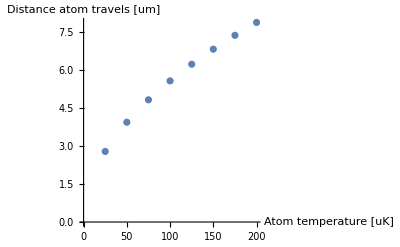

```mathematica
ListPlot[Table[{T/10^-6,(vRMS[T]*tFORTdrop)/10^-6},{T,Range[25*10^-6,200*10^-6,25*10^-6]}],AxesLabel-> {"Atom temperature [uK]","Distance atom travels [um]"}]
```

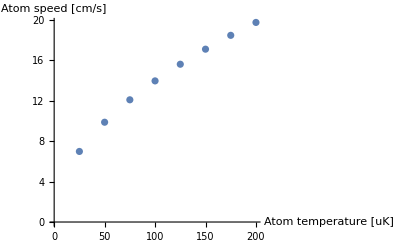

```mathematica
ListPlot[Table[{T/10^-6,vRMS[T]*100},{T,Range[25*10^-6,200*10^-6,25*10^-6]}],AxesLabel-> {"Atom temperature [uK]","Atom speed [cm/s]"}]
```

General escape velocity (speed)?

```mathematica
Fdip[r_]:=(-hbar Δ)/2(-2*I0*r ⅇ^(-r^2/w^2)/Isat)/(1+ (4 Δ^2)/γ^2+I0 ⅇ^(-r^2/w^2)/Isat);
```

```mathematica
Integrate[Fdip[r],{r,0,∞}]
```

```mathematica
ConditionalExpression[1/2 hbar w^2 Δ Log[1+(I0 γ^2)/(Isat γ^2+4 Isat Δ^2)],Re[w^2]>0]
```

```mathematica
Integrate[-Fdip[r],{r,rr,∞}]
```

$Aborted

```mathematica
Solve[1/2 m vEsc^2== 1/2 hbar w^2 Δ Log[1+(I0 γ^2)/(Isat γ^2+4 Isat Δ^2)],vEsc]
```

{{vEsc→-(√hbar w √Δ √Log[1+(I0 γ^2)/(Isat γ^2+4 Isat Δ^2)])/(√m)},{vEsc→(√hbar w √Δ √Log[1+(I0 γ^2)/(Isat γ^2+4 Isat Δ^2)])/(√m)}}

#### AC Stark Shifts and Trap Depth

5.6477+1.54604 x

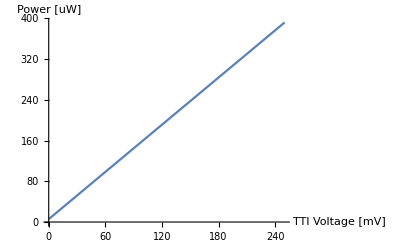

```mathematica
fit =5.6477+1.54604 x
Plot[fit,{x, 0,250},AxesLabel->{"TTI Voltage [mV]","Power [uW]"}]
```

```mathematica
NSolve[fit==250,x]
```

{{x→158.05}}

```mathematica
fit/.x->150
```

237.554

```mathematica
345.7765
```

Ground state shift

Polarizabilities obtained from Thad Walker.

For the 5p3/2 state 1064 nm light:

```mathematica
Clear[P,w0]
```

```mathematica
leakage = .05;(*percentage of total FORT power getting to atoms; e.g. leakage is about .05*)
```

```mathematica
α05pThreeHalves = 4 π ϵ0*10^-6*-143.77*10^-24;
α25pThreeHalves = 4 π ϵ0 *10^-6*74.44*10^-24; (*SI units*)
```

```mathematica
Uac[F_,mF_,J_,i_,E_,α0_,α2_]:= -1/4 α0 E^2-1/4 α2 E^2(3 mF^2-F(F+1))/(F(2F-1)) ((3 (F(F+1)+J(J+1)−i(i+1))((F(F+1)+J(J+1)−i(i+1)) - 1) - 4F(F+1)J(J+1))/((2 F +2)(2F+3) J (2 J -1)));
cgsToSI[α_]:=4π ϵ0*10^-6 α;
```

```mathematica
Efield[P_] := ((4P)/(c ϵ0 π w0^2))^(1/2);
```

```mathematica
P = .250*.4; 
w0 = 2.5*10^-6;
```

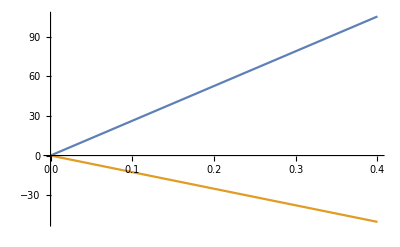

```mathematica
Plot[{JToMHz[Uac[3,0,3/2,3/2,Efield[.4*pow],α05pThreeHalves,α25pThreeHalves]],-JToMHz[1/4 α05sOneHalf Efield[.4*pow]^2]},{pow,0,.400}]
```

```mathematica
α05sOneHalf = cgsToSI[97*10^-24];
```

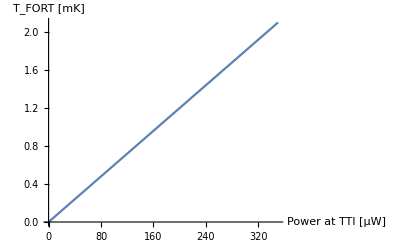

```mathematica
Plot[1/4 α05sOneHalf Efield[.4*pow]^2/kB,{pow,0,350},AxesLabel->{"Power at TTI [μW]","T_FORT [mK]"}]
```

```mathematica
1/4 α05sOneHalf Efield[.4*.250]^2/kB (*the ground state energy shift as a temp*)
```

0.00149941

```mathematica
NSolve[1/4 α05sOneHalf Efield[p*.4]^2/kB == .0024,p]
```

{{p→0.400158}}

AC Stark Shifts - D2 Line

```mathematica
DiffACShifts = Table[{mF,JToMHz[Uac[3,mF,3/2,3/2,Efield[.4*.400],α05pThreeHalves,α25pThreeHalves]]+JToMHz[1/4 α05sOneHalf Efield[.4*.400]^2]},{mF,-3,3}];
```

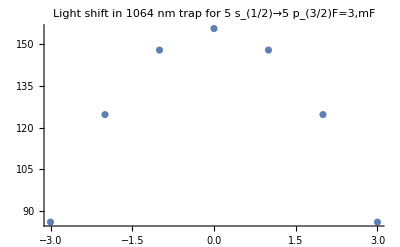

```mathematica
(*ListPlot[DiffACShifts,PlotRange->Full,PlotLabel->"Light shift in 1064 nm trap for 5 s_(1/2)→5 p_(3/2)F=3,mF"]*)
ListPlot[DiffACShifts,PlotRange->Full,PlotLabel->"Light shift in 1064 nm trap for 5 s_(1/2)→5 p_(3/2)F=3,mF"]
```

For different powers:

```mathematica
(*Table[ListPlot[Table[{mF,JToMHz[Uac[3,mF,3/2,3/2,Efield[.4*P],α05pThreeHalves,α25pThreeHalves]]-GroundStateShift},{mF,-3,3}]],{P,{.2,.3,.4,.5}}]*)
```

5p3/2

Shifts with only 5% power leaking through the AOM.

```mathematica
leakage = .05
```

0.05

```mathematica
ExcitedACShifts=Table[{mF,JToMHz[Uac[3,mF,3/2,3/2,Efield[leakage*P],α05pThreeHalves,α25pThreeHalves]]},{mF,-3,3}]
```

{{-3,1.71505},{-2,3.55652},{-1,4.6614},{0,5.02969},{1,4.6614},{2,3.55652},{3,1.71505}}

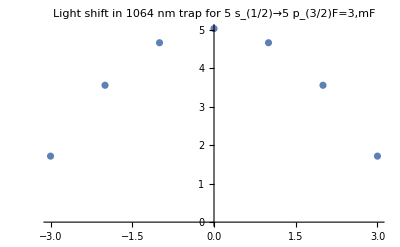

```mathematica
ListPlot[ExcitedACShifts,PlotRange->Full,PlotLabel->"Light shift in 1064 nm trap for 5 s_(1/2)→5 p_(3/2)F=3,mF"]
```

These Stark shifts are all positive so atoms left in the excited state will be repulsed by the FORT. When chopping the FORT and RO alternately it is critical that the RO light is turned off for at least one lifetime (~ .16 μs) of the excited state so that the atoms decay to the ground state before the FORT is turned back on.

#### Trap Depth

```mathematica
r2power = .4*.384 ;(*40% in 0 order, 384 mW measured before Jenoptik*)
```

```mathematica
GroundStateShiftJ = -1/4 α05sOneHalf Efield[r2power]^2(*[J]*)
```

-3.17987×10^-26

```mathematica
Tdepth = -1000*GroundStateShiftJ/kB (*the FORT "depth" in [mK]*)
```

2.30309

Mark’s example for Cs

```mathematica
Ef= ((4 (.01))/(c ϵ0 π (10^-6)^2))^(1/2);
```

```mathematica
-1/4 cgsToSI[(168*10^-24)] Ef^2
```

-2.24097×10^-26

```mathematica
Solve[α == (2 pt/(π w^2)RR^2)/(c e0 hb^2), pt]
```

{{pt→(c e0 hb^2 π w^2 α)/(2 RR^2)}}

Calculation of parabolic approximation to potential (for “small oscillations”)

Clear[ρ]
D[-Umax/(1+(z/zR)^2)Exp[-2 ρ^2 1/(w0^2(1+(z/zR)^2))],{z,2}]//FullSimplify
1/(w0^4 (z^2+zR^2)^5)2 ⅇ^(-(2 zR^2 ρ^2)/(w0^2 (z^2+zR^2))) Umax zR^2 (w0^4 (-3 z^2+zR^2) (z^2+zR^2)^2-2 w0^2 zR^2 (-7 z^2+zR^2) (z^2+zR^2) ρ^2-8 z^2 zR^4 ρ^4)
f=1/(w0^4 (z^2+zR^2)^5)2 ⅇ^(-(2 zR^2 ρ^2)/(w0^2 (z^2+zR^2))) Umax zR^2 (w0^4 (-3 z^2+zR^2) (z^2+zR^2)^2-2 w0^2 zR^2 (-7 z^2+zR^2) (z^2+zR^2) ρ^2-8 z^2 zR^4 ρ^4);
f/.z→0
(2 ⅇ^(-(2 ρ^2)/w0^2) Umax (w0^4 zR^6-2 w0^2 zR^6 ρ^2))/(w0^4 zR^8)